Шумы при сдвиге частот Δφ=0:
Через функции!

```mathematica
SVDVector[x_, a_?NumberQ] := Transpose[SingularValueDecomposition[x][[1; 3]]][[a]];
```

```mathematica
AbsFourier[x_]:=Abs[Take[Fourier[x,FourierParameters->{-1, 1}],{3,Round[Length[x]/2 ]+1}]]
```

```mathematica
NumPlace[x_]:=Position[AbsFourier[x],Max[AbsFourier[x]]][[1,1]]
```

```mathematica
FreqList[x_]:=Table[1.0*b/Length[x],{b,2,Length[x]-1}]
Freq[x_]:=FreqList[x][[NumPlace[x]]]
```

```mathematica
SetOptions[{Plot,ListPlot,ListLinePlot,ListLogPlot},PlotRange->Full,Axes->False,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],BaseStyle->{FontFamily->"Courier New",FontSize->15,Bold},ImageSize->600,PlotStyle->{Red,PointSize[0.01]}];
TruePlot[x_]:=ListPlot[Transpose[{FreqList[x][[NumPlace[x]-10;;NumPlace[x]+10]],AbsFourier[x][[NumPlace[x]-10;;NumPlace[x]+10]]}],FrameLabel->{"ν","A, mm"}]
FullPlot[x_]:=ListPlot[Transpose[{FreqList[x][[3;;Round[Length[x]/2 ]+1]],AbsFourier[x]}],FrameLabel->{"ν","A, mm"}]
```

```mathematica
Unprotect[Internal`EncodeCharacters];

Internal`EncodeCharacters[str_,enc_]:=Quiet[FromCharacterCode[ToCharacterCode[str],enc]]

SetDirectory[NotebookDirectory[]<>"data.06"]
```

D:\Документы\Diploma Mag\PCA\data.06

```mathematica
data1=Import["v2k_bpm_xy_1.sdds","Table","HeaderLines"->13];
data2=Import["v2k_bpm_xy_2.sdds","Table","HeaderLines"->13];
data3=Import["v2k_bpm_xy_3.sdds","Table","HeaderLines"->13];
data4=Import["v2k_bpm_xy_4.sdds","Table","HeaderLines"->13];
```

```mathematica
Data1 = Transpose[data1][[3]];
Data1=Data1-Mean@Data1;
Data2 = Transpose[data2][[3]];
Data2=Data2-Mean@Data2;
Data3 = Transpose[data3][[3]];
Data3=Data3-Mean@Data3;
Data4 = Transpose[data4][[3]];
Data4=Data4-Mean@Data4;
Data5 =RotateLeft@Transpose[data1][[3]];
Data5 = Data1[[2;;Length[Data1]]];
Data5=AppendTo[Data5, RandomReal[Abs[Data5[[Length[Data5]]]]]];
Data5=Data5-Mean@Data5;
Data6 =RotateLeft@Transpose[data2][[3]];
Data6 = Data2[[2;;Length[Data2]]];
Data6 =AppendTo[Data6, RandomReal[Abs[Data6[[Length[Data6]]]]]];
Data6=Data6-Mean@Data6;
Data7 =RotateLeft@Transpose[data3][[3]];
Data7 = Data3[[2;;Length[Data3]]];
Data7 =AppendTo[Data7, RandomReal[Abs[Data7[[Length[Data7]]]]]];
Data7=Data7-Mean@Data7;
Data8 =RotateLeft@Transpose[data4][[3]];
Data8 = Data4[[2;;Length[Data4]]];
Data8 =AppendTo[Data8, RandomReal[Abs[Data8[[Length[Data8]]]]]];
Data8=Data8-Mean@Data8;
```

```mathematica
SigM=List[Data1,Data2,Data3,Data4, Data5, Data6, Data7, Data8];
```

0.170839

0.00256442

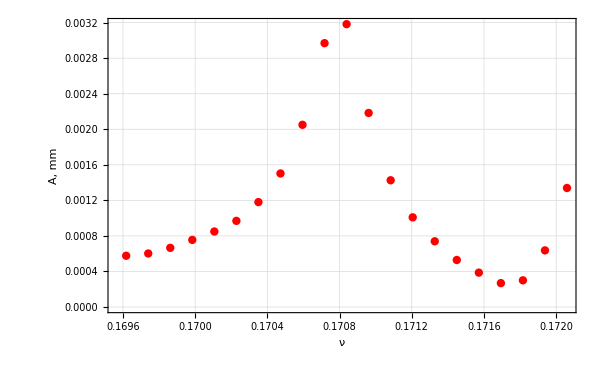

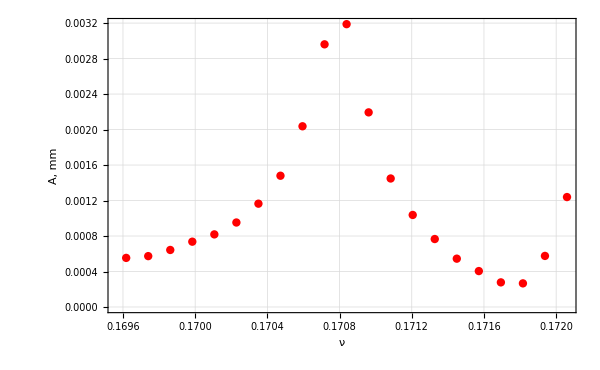

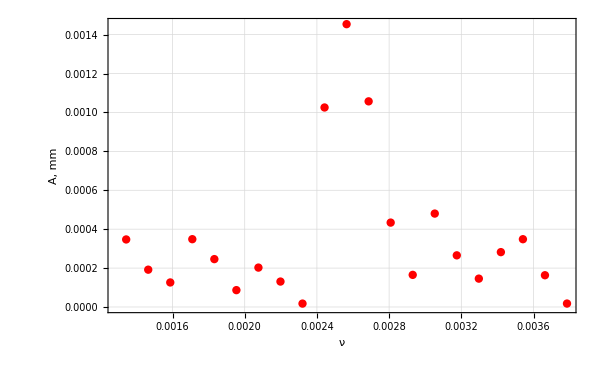

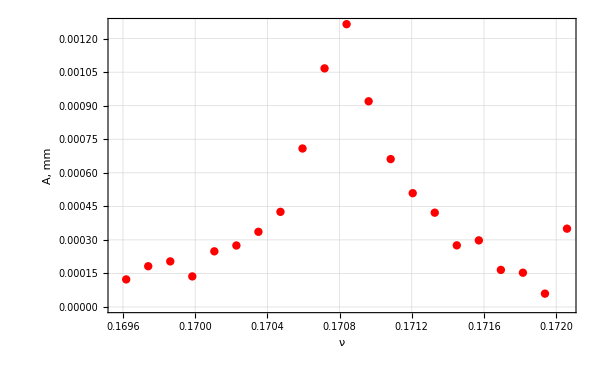

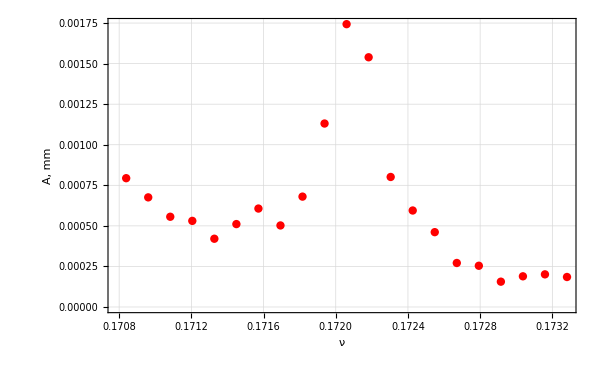

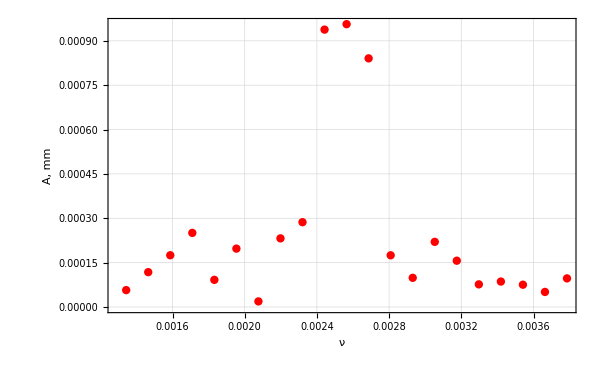

```mathematica
SVDVector1=SVDVector[SigM,1];
SVDVector2=SVDVector[SigM,2];
SVDVector3=SVDVector[SigM,3];
SVDVector4=SVDVector[SigM,4];
SVDVector5=SVDVector[SigM,5];
SVDVector6=SVDVector[SigM,6];
Freq[SVDVector1]
Freq[SVDVector3]
(*SVDPlot1=ListPlot[SVDVector1,Joined->True,PlotRange->All,FrameLabel->{"N","A, mm"}]
SVDPlot2=ListPlot[SVDVector2,Joined->True,PlotRange->All,FrameLabel->{"N","A, mm"}]
SVDPlot3=ListPlot[SVDVector3,Joined->True,PlotRange->All,FrameLabel->{"N","A, mm"}]

sigPlot=ListPlot[Data1,Joined->True,PlotRange->All]*)
TrueSVD1=TruePlot[SVDVector1]
TrueSVD2=TruePlot[SVDVector2]
TrueSVD3=TruePlot[SVDVector3]
TrueSVD4=TruePlot[SVDVector4]
TrueSVD5=TruePlot[SVDVector5]
TrueSVD6=TruePlot[SVDVector6]
```

0.170839

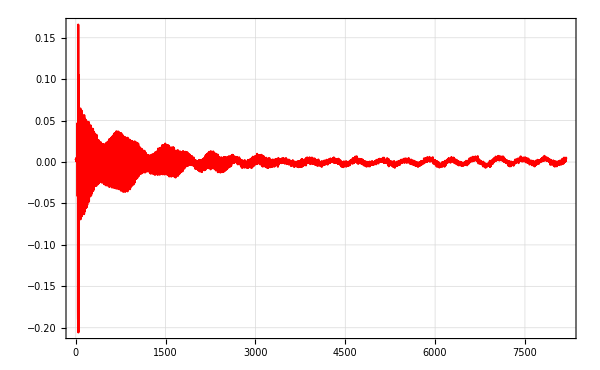

-Graphics-

```mathematica
SVDVector1=SVDVector[SigM,1];
Freq[SVDVector1]
ListPlot[SVDVector1,Joined->True,PlotRange->All]
TrueSVD1=TruePlot[SVDVector1]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Документы\Diploma Mag\PCA

0.17206

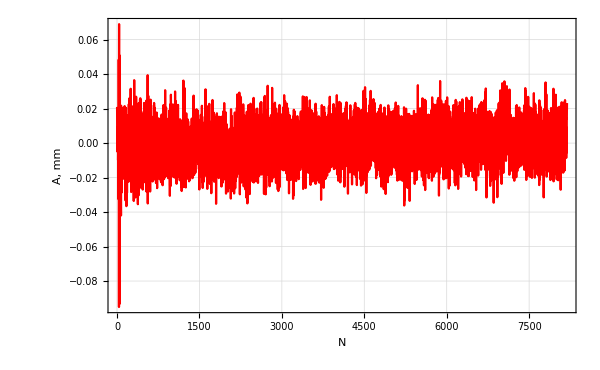

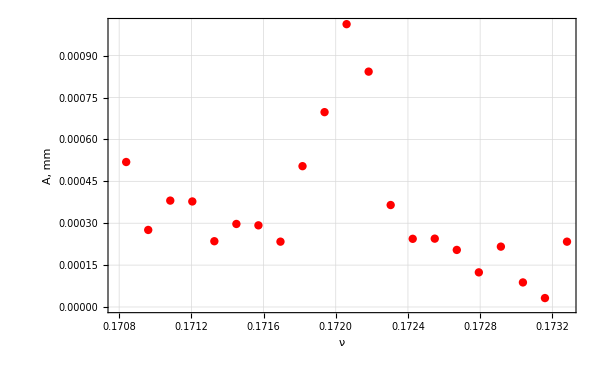

```mathematica
SVDVector7=SVDVector[SigM,7];
Freq[SVDVector7]
SVDPlot7=ListPlot[SVDVector7,Joined->True,PlotRange->All,FrameLabel->{"N","A, mm"}]
TrueSVD7=TruePlot[SVDVector7]
```

0.170839

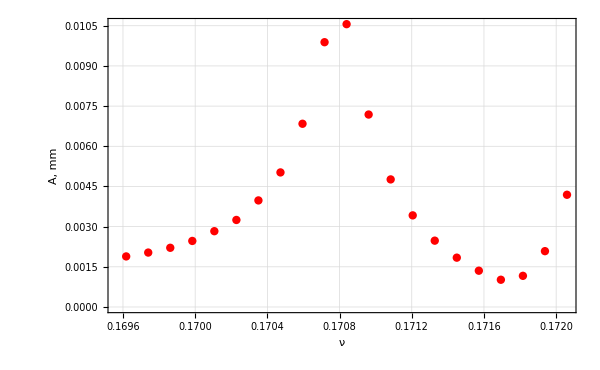

```mathematica
Freq[Data1]
Truesig=TruePlot[Data1]
```

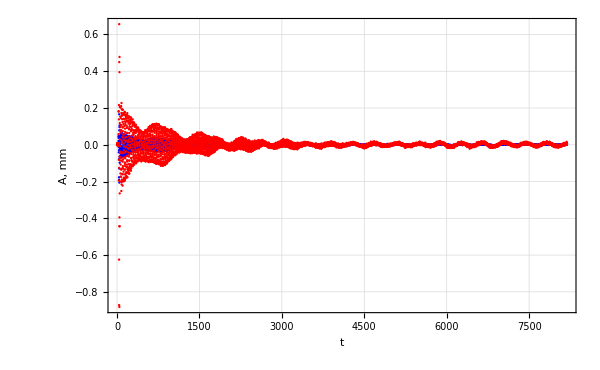

```mathematica
DobPCA=ListPlot[{SVDVector1,Data1},PlotStyle->{Blue,Red},FrameLabel->{"t","A, mm"}]
```

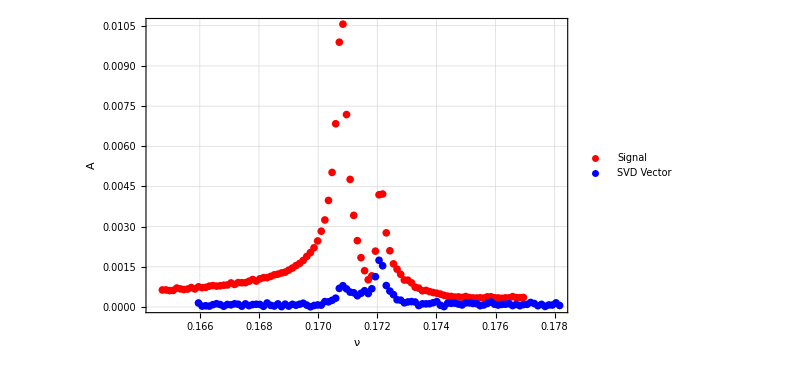

```mathematica
FulMasSig=Transpose[{FreqList[Data1][[NumPlace[Data1]-50;;NumPlace[Data1]+50]],AbsFourier[Data1][[NumPlace[Data1]-50;;NumPlace[Data1]+50]]}];
FulMasSVD5 =Transpose[{FreqList[SVDVector5][[NumPlace[SVDVector5]-50;;NumPlace[SVDVector5]+50]],AbsFourier[SVDVector5][[NumPlace[SVDVector5]-50;;NumPlace[SVDVector5]+50]]}];
DobFourPCA=ListPlot[{FulMasSig,FulMasSVD5},PlotStyle->{Red,Blue}, PlotLegends->Placed[{"Signal","SVD Vector"},{Scaled[{0.95,0.7}],{0.95,0.7}}],FrameLabel->{"ν","A"}]
```

```mathematica
Export["DobFourPCA.png",DobFourPCA]
```

DobFourPCA.png

```mathematica
Export["DobPCA.png",DobPCA]
```

DobPCA.png

```mathematica
image = {{DobPCA, TrueSVD1,TrueSVD3, TrueSVD5}}
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Export["decomposition.png", image]
```

decomposition.png

D:\Документы\Diploma Mag\PCA\data.06

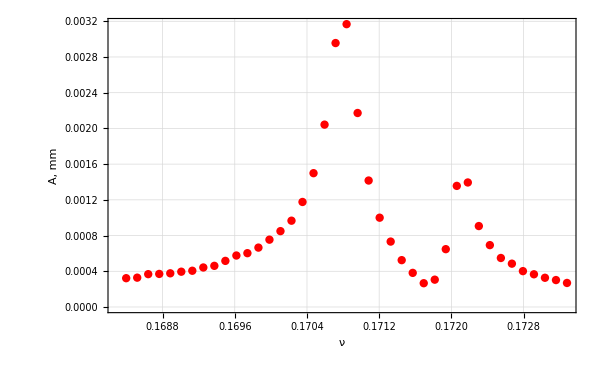

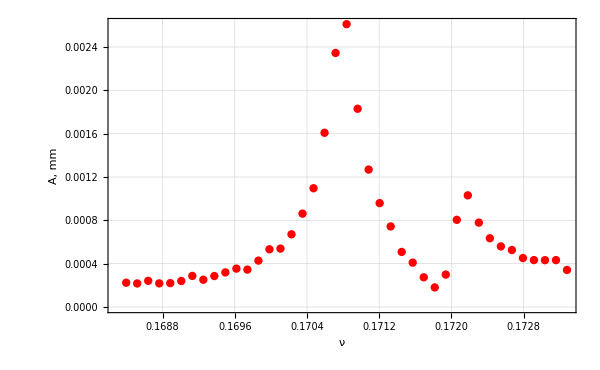

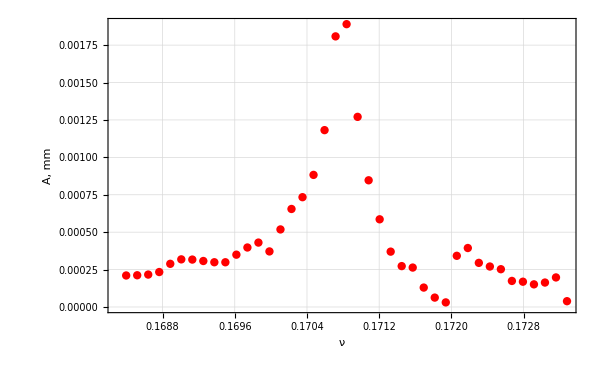

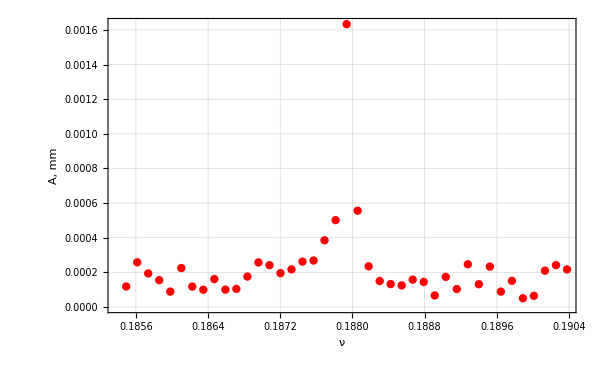

```mathematica
SetDirectory[NotebookDirectory[]<>"data.06"]
SigMNoAdd=List[Data1,Data2,Data3,Data4];
For[i=1,i<5,i++,Print[TruePlot[SVDVector[SigMNoAdd, i]]]]
```

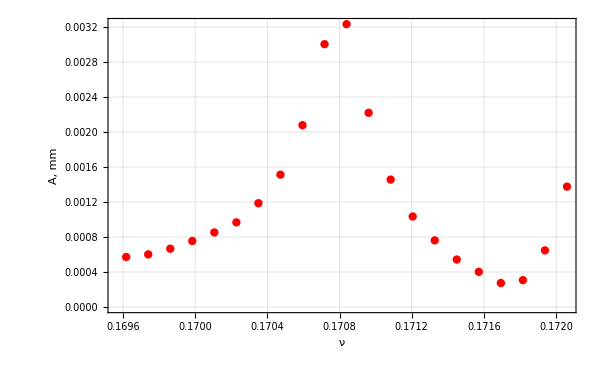

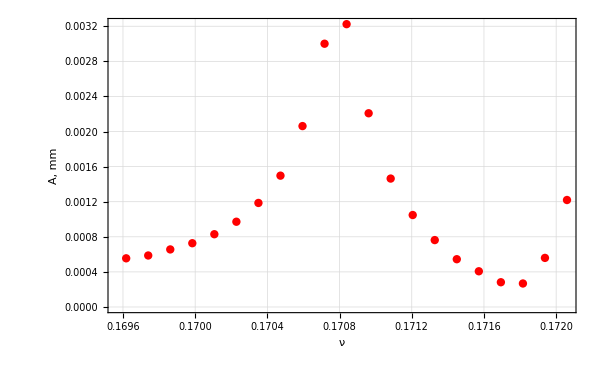

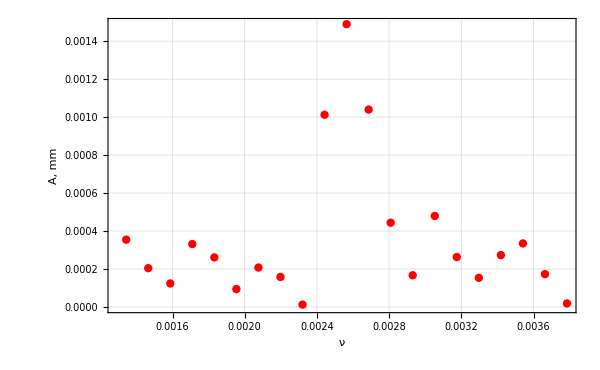

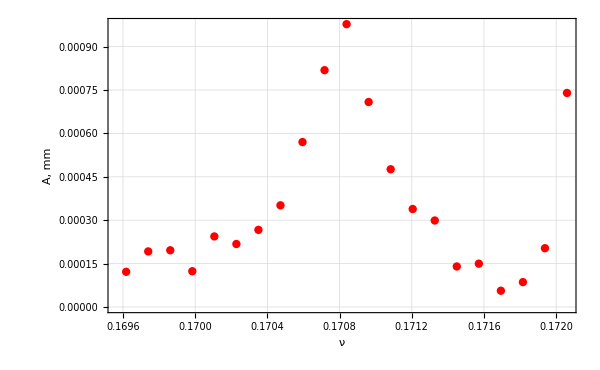

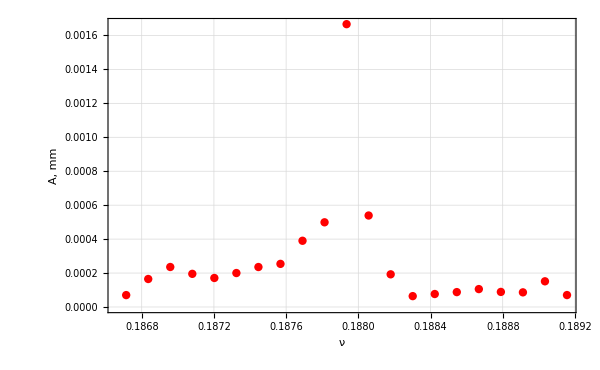

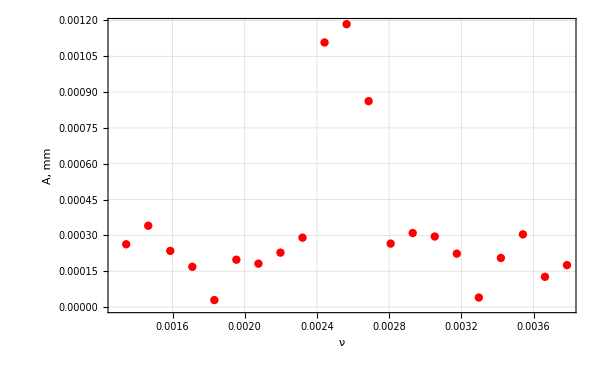

```mathematica
SigM2=List[Data1,Data2,Data3,Data4, Data5, Data6];
For[i=1,i<7,i++,Print[TruePlot[SVDVector[SigM2, i]]]]
```

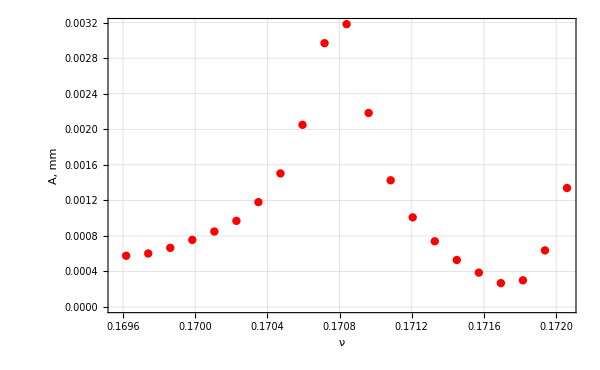

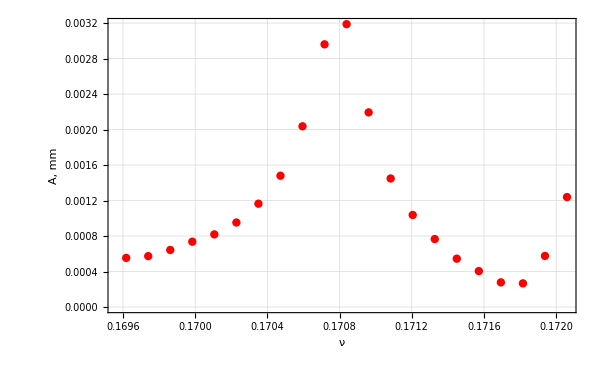

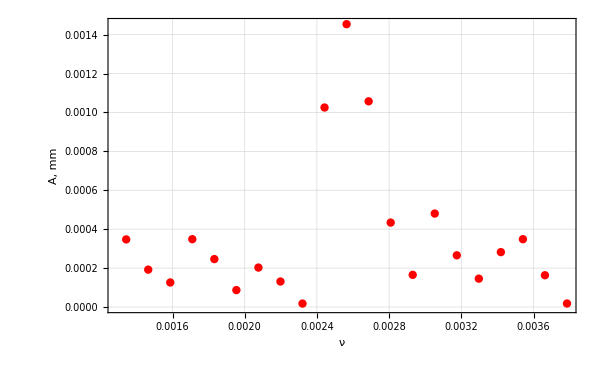

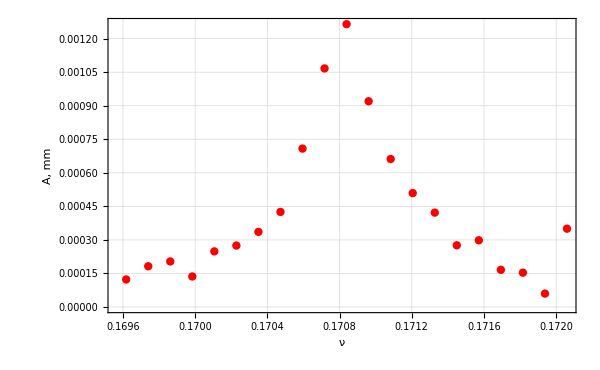

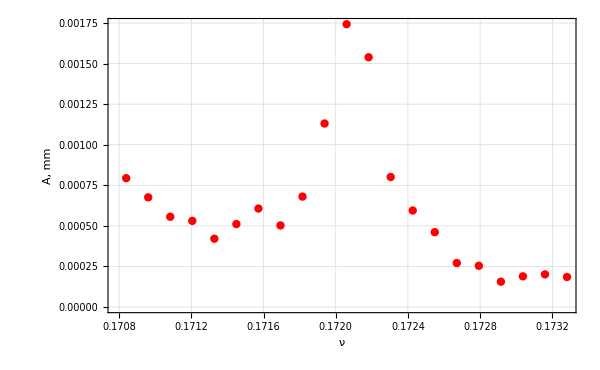

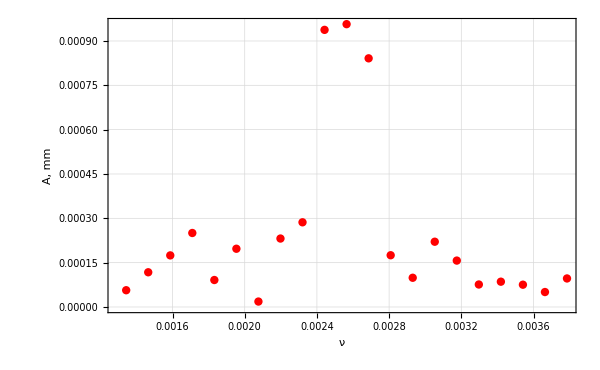

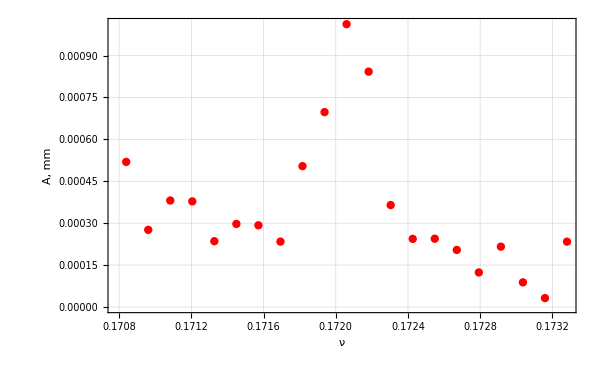

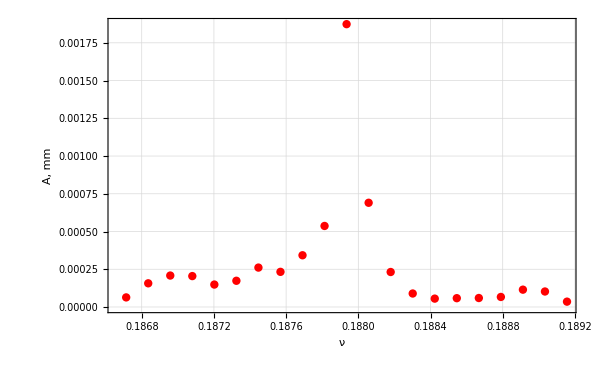

```mathematica
For[i=1,i<9,i++,Print[TruePlot[SVDVector[SigM, i]]]]
```